# Compiling Matmul to Blocks and Tiles

## Technical Report, Preliminary Draft, GSI Technology

Brian Beckman
Technology Fellow
November, 2023

## Abstract

The layout problem answers “how to rearrange matrices to fit the APU?” Consider domain matrices, A[m,k] and B[k,n], of arbitrary but compatible dimensions, meaning that the column count, k, of A equals the row count, k, of B. Due to compatibility, the matrix product A.B is sensible. Now consider the Gemini-I APU, which has a main memory (MMB) of 24×VR bits, where a VR is 64 HBs and an HB (half-bank) is 2048×16 bits. The Gemini-I APU also has 53 VRs worth of space in L1 cache (parity off). The layout problem for matrix multiplication is finding an optimal procedure for dynamically loading to, multiplying in, and storing from chunks of A and B in the APU’s L1 cache and main memory. The solution to the layout problem includes finding optimal sizes of chunks and optimal sequences of operations for moving and multiplying data. Optimal means minimum running time. Compile time is not considered. Running time includes the time for I/O between L1 and main memory.

At first glance, the layout problem seems like a constrained combinatorial optimization problem, thus difficult to pose well and expensive to solve. This paper by Kuzma et al. presents an approach wherein the compiler breaks up input domain matrices into blocks and tiles. Blocks are optimized to fit L1, tiles are optimized to fit main memory, where multiplication occurs. We investigate and mechanize Kuzma’s algorithm in this paper, first by reproducing Kuzma’s original example, then by adapting that example to the APU.

## Accumulated Outer Product

First, we note that accumulated outer product is preferable to iterated inner product for all dimensions >1. This fact justifies the inner-most routine shown below, tileMul.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
```

### Large Matrices

```mathematica
ClearAll[timings];
(timings=With[{precision=1*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,200,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 6.×10^-6 s | 0.000017 s | 0.000014 s
26 | 0.000017 s | 0.001631 s | 0.000081 s
51 | 0.000012 s | 0.007707 s | 0.000224 s
76 | 0.000246 s | 0.028926 s | 0.000678 s
101 | 0.000057 s | 0.064556 s | 0.001203 s
126 | 0.000101 s | 0.105207 s | 0.002689 s
151 | 0.000079 s | 0.176309 s | 0.004262 s
176 | 0.000173 s | 0.246875 s | 0.005999 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

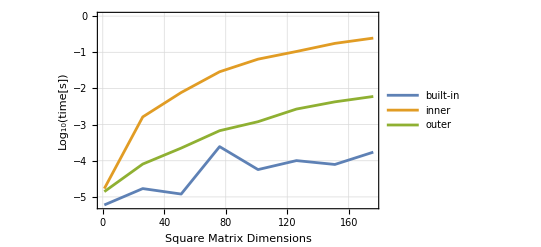

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```

## Table 1 — VSR and ACC

Kuzma presents a worked-out example for his IBM POWER10 MMA chip, which has VSRs of 128 bits and ACCs of 512 bits. The bits in these registers can handle seven different types of elements.

```mathematica
ClearAll[mmaI,mmaI4,mmaI8,mmaI16,mmaBf16,mmaF16,mmaF32,mmaF64];
```

The integer MMA instructions for the POWER10 consume four 128-bit VSRs — an ACC, for a total of 512 bits. Up to 32 VSRs can be used, 4 at a time, in this way.

```mathematica
mmaI[bitCount_?(MemberQ[{4,8,16},#]&)]:=
With[{m=4,k=32/bitCount,n=4},
With[{A=RandomInteger[{0,2^bitCount-1},{m,k}],
B=RandomInteger[{0,2^bitCount-1},{k,n}]},
accumulatedOuterProduct[m,k,n,A,B]]]
```

```mathematica
mmaI[8]
```

<|m→4,k→4,n→4,result→{{41791,59966,26744,58644},{73272,18786,81268,89405},{67764,43219,60270,79047},{87364,58778,65428,103566}},time→0.00004 s|>

accumulatedOuterProduct also works as a rank-1 outer product.

```mathematica
accumulatedOuterProduct[5,1,4,({{1}, {2}, {3}, {4}, {5}}),({{7, 11, 13, 19}})]["result"]//MatrixForm
```

(7 | 11 | 13 | 19
14 | 22 | 26 | 38
21 | 33 | 39 | 57
28 | 44 | 52 | 76
35 | 55 | 65 | 95)

## Codegen for GEMM

GEMM is a standard operation in LAPACK.

### Algorithm 1

A, B, APack, BPack, AccTile, ATile, BTile, ABTile, CTile, and CNewTile are free-variable pointers to memory. nr , kr, mr are free packing parameters. In my opinion, they would be better called tiling parameters because they’re tuned to the intrinsic LLVM on line 12, but I’ll follow the paper’s nomenclature for now. nc, kc, mc are free blocking parameters that divide matrices into blocks appropriately sized and ordered (row-major versus column-order) for cache. lda, ldb, ldc are free leading dimensions, thus strides, and pertain to either row-major or column-major storage conventions. The pack function reorders blocks into row-major or column-major order as needed for optimal tile-multiplication speed. α and β are free scalar parameters required by GEMM.

```mathematica
ClearAll[packingParameters,mr,kr,nr,blockingParameters,mc,kc,nc,A,APack,B,BPack,leadingDimensions,lda,ldb,ldc,ATile,BTile,AccTile,ABTile,CTile,CNewTile,β,α];
packingParameters={mr,kr,nr};
blockingParameters={mc,kc,nc};
leadingDimensions={lda,ldb,ldc};
```

M, K, N are original dimensions: M×K for AOriginal, K×N for BOriginal. kc (block size) must divide K; mc (block size) must divide M, nc (block size) must divide N. If not, the original matrices, AOriginal and BOriginal, must be padded out with zeros to integer multiples of mc, kc, nc. Such is preprocessing, not described here.

In the following illustration, AOriginal and BOriginal are stored in column-major order.

Let us mechanize a concrete version of this illustration by ignoring most ellipses (triple dots). An exception is the picture of B, for which we increase kc from 2kr to 3kr for consistency with the picture of A. The two pictures for A and for B represent the (4,2) and (2,2) 1-indexed blocks, respectively, of the original matrices, AOriginal and BOriginal.

## Compiling MatMul to Blocks and Tiles

### tileMul

Everything gets compiled to calls of tileMul.

tileMul multiplies blocks that contain small tiles, multiplying each tile at maximum speed in the machine. A tile is a sub-matrix that snugly fits in the particular machine registers that are necessary for multiplication. tileMul is here parameterized to the dimensions of blocks and tiles so that we can compile to various devices, such as the Gemini-I APU and the Gemini-II APU, which differ in dimensions.

tileMul takes a pair of blocks with tiles inside, then triples of inner and outer dimensions. The three outer dimensions, mc, kc, and nc, correspond to the dimensions of block multiplicands, mc×kc and kc×nc. The three inner dimensions, mr, kr, and nr, correspond to dimensions of tile multiplicands, namely mr×kr and kr×nr. Each outer dimension must be evenly divisible by the corresponding inner dimension, meaning that tiles must fit blocks with no gaps or overlaps. The number of block rows must be an integer multiple of the number of tile rows, and likewise for columns. Each of mc/mr, kc/kr, and nc/nr must be integers.

As an illustration, consider the following two tiled blocks:

```mathematica
aBlockTiled$=({{({{15, 14, 10, 15}, {3, 9, 8, 5}}), ({{6, 0, 3, 8}, {5, 10, 9, 6}}), ({{3, 14, 1, 1}, {6, 1, 14, 4}})}, {({{11, 14, 9, 10}, {11, 13, 3, 3}}), ({{12, 2, 0, 15}, {5, 3, 15, 13}}), ({{5, 4, 14, 1}, {13, 4, 7, 3}})}, {({{12, 7, 14, 14}, {15, 6, 14, 13}}), ({{2, 7, 15, 15}, {1, 13, 0, 8}}), ({{5, 0, 9, 1}, {14, 5, 2, 10}})}});
bBlockTiled$=({{({{9, 4}, {4, 1}, {11, 9}, {15, 3}}), ({{9, 13}, {14, 12}, {9, 13}, {12, 13}}), ({{6, 7}, {7, 11}, {10, 3}, {7, 15}}), ({{12, 3}, {8, 4}, {0, 13}, {3, 12}}), ({{4, 11}, {8, 11}, {5, 4}, {5, 5}})}, {({{13, 15}, {14, 2}, {0, 13}, {10, 0}}), ({{7, 0}, {10, 15}, {3, 15}, {8, 7}}), ({{1, 4}, {6, 6}, {15, 6}, {11, 7}}), ({{15, 5}, {11, 6}, {15, 6}, {11, 11}}), ({{5, 8}, {14, 10}, {8, 15}, {5, 15}})}, {({{3, 14}, {10, 10}, {7, 5}, {10, 8}}), ({{0, 3}, {14, 5}, {6, 1}, {0, 3}}), ({{5, 3}, {9, 7}, {13, 2}, {14, 12}}), ({{5, 2}, {11, 15}, {1, 10}, {7, 5}}), ({{9, 12}, {11, 0}, {2, 7}, {8, 6}})}});
```

The outer dimensions of the pair (aBlockTiled$, bBlockTiled$) are mc=(3×(mr=2))=6 (three rows of 2-row tiles in aBlockTiled$), kc=(3×(kr=4))=12 (three columns of 4-column tiles in aBlockTiled$, and three rows of 4-row tiles in bBlockTiled$), and nc=(5×(nr=2))=10 (five columns of 2-column tiles in bBlockTiled$). The inner dimensions are mr=2, kr=4, nr=2, corresponding respectively to the row dimension, mr, of a left-multiplicand tile; to the column dimension, kr, of a left-multiplicand tile, equal to the row dimension of a right-multiplicand tile; and to the column dimension, nr, of a right-multiplicand tile.

Let’s define tileMul, then apply it to these examples:

```mathematica
ClearAll[tileMul];
tileMul[ATiles_,BTiles_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{tm,tk,tn,CTile,McByMr=mc/mr,KcByKr=kc/kr,NcByNr=nc/nr},
CTile=ConstantArray[ConstantArray[0,{mr,nr}],{McByMr,NcByNr}];
For[tm=1,tm<=McByMr,tm++,
For[tn=1,tn<=NcByNr,tn++,
For[tk=1,tk<=KcByKr,tk++,
(* accumulated outer product *)
CTile[[tm,tn]]+=ATiles[[tm,tk]].BTiles[[tk,tn]]]]];
CTile];
```

```mathematica
tileMul[aBlockTiled$,bBlockTiled$,6,12,10,2,4,2]//MatrixForm
```

((850 | 533
657 | 516) | (918 | 872
593 | 692) | (700 | 733
739 | 496) | (737 | 778
592 | 601) | (582 | 696
541 | 748)
(901 | 541
624 | 650) | (860 | 745
656 | 813) | (770 | 656
833 | 610) | (731 | 778
858 | 607) | (539 | 866
629 | 1004)
(862 | 585
989 | 608) | (803 | 1066
784 | 968) | (949 | 703
811 | 747) | (780 | 826
710 | 751) | (618 | 1000
735 | 852))

### untileBlock

Is this equal to the matrix product aBlockTiled$.bBlockTiled$ when the tile boundaries are removed? To check, let’s first define untileBlock, which does exactly what its name says.

```mathematica
ClearAll[untileBlock];
untileBlock[ATiledBlock_,mr_,mc_,kr_,kc_]:=
(* Produce 1 mc×kc block from its tiles, each mr×kr. *)
Module[{ABlock=ConstantArray[0,{mc,kc}],tileI,tileJ,inI,inJ,bm,bk},
For[bm=1,bm<=mc,bm++,
For[bk=1,bk<=kc,bk++,
tileI=1+Quotient[(bm-1),mr];
tileJ=1+Quotient[(bk-1),kr];
inI=1+Mod[(bm-1),mr];
inJ=1+Mod[(bk-1),kr];
ABlock[[bm,bk]]=ATiledBlock[[tileI,tileJ,inI,inJ]]]];
ABlock];
```

Apply untileBlock to aBlockTiled$ and to bBlockTiled$., compute the matrix product via Wolfram’s built-in, then visually check that the untiled matrices match their tiled brethren above.

```mathematica
(aBlock$=untileBlock[aBlockTiled$,2,6,4,12])//MatrixForm
(bBlock$=untileBlock[bBlockTiled$,4,12,2,10])//MatrixForm
(cBlock$=aBlock$.bBlock$)//MatrixForm
```

(15 | 14 | 10 | 15 | 6 | 0 | 3 | 8 | 3 | 14 | 1 | 1
3 | 9 | 8 | 5 | 5 | 10 | 9 | 6 | 6 | 1 | 14 | 4
11 | 14 | 9 | 10 | 12 | 2 | 0 | 15 | 5 | 4 | 14 | 1
11 | 13 | 3 | 3 | 5 | 3 | 15 | 13 | 13 | 4 | 7 | 3
12 | 7 | 14 | 14 | 2 | 7 | 15 | 15 | 5 | 0 | 9 | 1
15 | 6 | 14 | 13 | 1 | 13 | 0 | 8 | 14 | 5 | 2 | 10)

(9 | 4 | 9 | 13 | 6 | 7 | 12 | 3 | 4 | 11
4 | 1 | 14 | 12 | 7 | 11 | 8 | 4 | 8 | 11
11 | 9 | 9 | 13 | 10 | 3 | 0 | 13 | 5 | 4
15 | 3 | 12 | 13 | 7 | 15 | 3 | 12 | 5 | 5
13 | 15 | 7 | 0 | 1 | 4 | 15 | 5 | 5 | 8
14 | 2 | 10 | 15 | 6 | 6 | 11 | 6 | 14 | 10
0 | 13 | 3 | 15 | 15 | 6 | 15 | 6 | 8 | 15
10 | 0 | 8 | 7 | 11 | 7 | 11 | 11 | 5 | 15
3 | 14 | 0 | 3 | 5 | 3 | 5 | 2 | 9 | 12
10 | 10 | 14 | 5 | 9 | 7 | 11 | 15 | 11 | 0
7 | 5 | 6 | 1 | 13 | 2 | 1 | 10 | 2 | 7
10 | 8 | 0 | 3 | 14 | 12 | 7 | 5 | 8 | 6)

(850 | 533 | 918 | 872 | 700 | 733 | 737 | 778 | 582 | 696
657 | 516 | 593 | 692 | 739 | 496 | 592 | 601 | 541 | 748
901 | 541 | 860 | 745 | 770 | 656 | 731 | 778 | 539 | 866
624 | 650 | 656 | 813 | 833 | 610 | 858 | 607 | 629 | 1004
862 | 585 | 803 | 1066 | 949 | 703 | 780 | 826 | 618 | 1000
989 | 608 | 784 | 968 | 811 | 747 | 710 | 751 | 735 | 852)

### blockIt, tileIt

We now know how to multiply blocks full of snug tiles. We need, from general matrices, to produce matrices full of snug block, in-turn full of snug tiles. The dimensions of the snug blocks must divide the dimensions of the matrices, but that is the only restriction. If the matrices don’t snugly contain blocks, pad out the matrices in a pre-processing step. We do not consider that step in this paper.

Define a pair of functions, blockIt and tileIt, that, respectively, produce a blocked matrix and a tiled block.

```mathematica
ClearAll[blockIt,tileIt];

blockIt[A_,mc_,M_,kc_,K_]:=Table[
A[[m;;m+mc-1,k;;k+kc-1]],{m,1,M,mc},{k,1,K,kc}];

tileIt[ABlock_,mr_,mc_,kr_,kc_]:=Table[
ABlock[[m;;m+mr-1,k;;k+kr-1]],{m,1,mc,mr},{k,1,kc,kr}];
```

Iterate tileIt over the result of blockIt on an (appropriately padded, but not here) matrix to get a fully blocked and tiled matrix. Here is an example. Notice we build the dimensions bottom-up to ensure integer divisibility and thus avoid padding. The regular structure is evident and instructive. Strive to see how 2D iterations of tileMul produces desired results.

```mathematica
With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=2mr,kc=2kr,nc=2nr},(* mc=4, kc=8, nc=4 -- blocks *)
With[{M=2mc,K=2kc,N=2nc},(* M=8, K=16, N=8, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocked=blockIt[A,mc,M,kc,K],
BBlocked=blockIt[B,kc,K,nc,N],
ATiled,BTiled},
ATiled=Table[tileIt[ABlocked[[bm,bk]],mr,mc,kr,kc],{bm,1,M/mc},{bk,1,K/kc}];
BTiled=Table[tileIt[BBlocked[[bk,bn]],kr,kc,nr,nc],{bk,1,K/kc},{bn,1,N/nc}];
Column[{(* displays *)
ATiled//MatrixForm,
BTiled//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[A_blocked]"->Dimensions[ABlocked],
"dim[B_blocked]"->Dimensions[BBlocked],
"A_tiled"->Dimensions[ATiled],
"B_tiled"->Dimensions[BTiled],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{8,16},dim[B]→{16,8},dim[A_blocked]→{2,2,4,8},dim[B_blocked]→{2,2,8,4},A_tiled→{2,2,2,2,2,4},B_tiled→{2,2,2,2,4,2},bits→4,mr→2,kr→4,nr→2,mc→4,kc→8,nc→4,M→8,K→16,N→8|>

(((6 | 11 | 3 | 7
4 | 14 | 15 | 14) | (14 | 7 | 11 | 1
12 | 1 | 10 | 3)
(15 | 7 | 12 | 9
13 | 2 | 4 | 2) | (12 | 9 | 3 | 5
2 | 6 | 6 | 7)) | ((15 | 0 | 10 | 4
7 | 13 | 7 | 4) | (2 | 14 | 3 | 14
0 | 5 | 0 | 8)
(4 | 4 | 2 | 12
9 | 6 | 12 | 12) | (1 | 5 | 13 | 14
6 | 14 | 4 | 1))
((3 | 8 | 13 | 3
8 | 9 | 12 | 0) | (5 | 12 | 6 | 11
10 | 3 | 13 | 0)
(14 | 5 | 7 | 12
3 | 4 | 5 | 4) | (6 | 3 | 15 | 5
12 | 5 | 15 | 0)) | ((3 | 8 | 1 | 9
6 | 1 | 14 | 6) | (4 | 1 | 7 | 4
14 | 3 | 1 | 6)
(5 | 10 | 14 | 2
10 | 14 | 10 | 11) | (2 | 15 | 2 | 14
3 | 7 | 2 | 0)))
(((3 | 5
7 | 10
5 | 1
8 | 9) | (3 | 14
8 | 9
8 | 14
10 | 9)
(14 | 1
1 | 0
9 | 10
0 | 10) | (4 | 7
5 | 7
15 | 10
12 | 13)) | ((4 | 1
12 | 14
11 | 4
9 | 15) | (4 | 8
11 | 13
10 | 12
4 | 9)
(13 | 13
13 | 2
14 | 14
3 | 6) | (5 | 14
0 | 5
14 | 4
6 | 4))
((2 | 9
3 | 10
6 | 1
3 | 9) | (7 | 7
14 | 5
10 | 11
8 | 5)
(3 | 6
11 | 10
14 | 8
14 | 7) | (13 | 13
6 | 14
15 | 10
3 | 4)) | ((9 | 5
7 | 7
9 | 2
6 | 6) | (11 | 3
12 | 10
9 | 3
5 | 15)
(8 | 14
9 | 9
12 | 7
13 | 9) | (9 | 3
12 | 9
3 | 12
8 | 13)))

### unBlock

unBlock is exactly parallel to untileBlock. It does not need a unit test or an illustrative example.

```mathematica
ClearAll[unblock];

unblock[ABlocked_,mc_,M_,kc_,K_]:=
Module[{A=ConstantArray[0,{M,K}],blockI,blockJ,inI,inJ,m,k},
For[m=1,m<=M,m++,
For[k=1,k<=K,k++,
blockI=1+Quotient[(m-1),mc];
blockJ=1+Quotient[(k-1),kc];
inI=1+Mod[(m-1),mc];
inJ=1+Mod[(k-1),kc];
A[[m,k]]=ABlocked[[blockI,blockJ,inI,inJ]]]];
A];
```

### blockTileMul, blockMul

blockTileMul is the intermediate target of compilation, after matrices have been blocked and tiled as described above. We include a blockMul routine for testing: the untiled results of blockTileMul must match the results of blockMul, and the unblocked results must match the results of Mathematica’s built-in matrix multiplication. The following defines blockTileMul and blockMul, then Asserts the requirements on an example.

```mathematica
On[Assert];
ClearAll[blockMul,blockTileMul];

blockTileMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
(* ABlocks is an array of mc×kc blocks, BBlock of kc×nc blocks. *)
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CTiled,ATiles,BTiles},
CTiled=ConstantArray[ConstantArray[ConstantArray[0,{mr,nr}],
{McByMr,NcByNr}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* accumulated outer product *)
For[bk=1,bk<=KByKc,bk++,
ATiles=tileIt[ABlocks[[bm,bk]],mr,mc,kr,kc];
BTiles=tileIt[BBlocks[[bk,bn]],kr,kc,nr,nc];
CTiled[[bm,bn]]+=tileMul[ATiles,BTiles,mc,kc,nc,mr,kr,nr]]]];
CTiled];

blockMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CBlocked},
CBlocked=ConstantArray[ConstantArray[0,{mc,nc}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* accumulated outer product *)
For[bk=1,bk<=KByKc,bk++,
CBlocked[[bm,bn]]+=ABlocks[[bm,bk]].BBlocks[[bk,bn]]]]];
CBlocked];

With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=6, kc=12, nc=10 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=30, K=36, N=30, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
A//MatrixForm;
ABlocks//MatrixForm;
BBlocks//MatrixForm;
CTiled//MatrixForm,
CBlockedCheck//MatrixForm;
CBlocked//MatrixForm;
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;
(*griddit[A,mc,M,kc,K],*)
(*griddit[B,kc,K,nc,N]*)}]]]]]]]
```

<|dim[A]→{30,36},dim[B]→{36,30},dim[C_tiled]→{5,3,3,5,2,2},dim[A_blocks]→{5,3,6,12},dim[B_blocks]→{3,3,12,10},dim[C]→{30,30},bits→4,mr→2,kr→4,nr→2,mc→6,kc→12,nc→10,M→30,K→36,N→30|>

(((2367 | 2420
2335 | 2611) | (2047 | 2687
2174 | 2965) | (2066 | 2126
2460 | 2413) | (1997 | 2142
1977 | 2409) | (1830 | 2480
2194 | 2690)
(1947 | 2556
2213 | 2614) | (2116 | 2388
1968 | 2610) | (2050 | 1954
2303 | 2105) | (1967 | 1923
1951 | 1968) | (1802 | 2593
1839 | 2473)
(1684 | 2236
2332 | 2235) | (1755 | 1980
1886 | 2579) | (1849 | 1910
2105 | 1940) | (1684 | 1471
1777 | 2086) | (1626 | 2028
1717 | 2491)) | ((1847 | 1917
1726 | 2166) | (2099 | 2220
2126 | 2637) | (1538 | 1725
1596 | 2116) | (2352 | 2329
2523 | 2439) | (1940 | 1764
2297 | 1686)
(1619 | 1943
1520 | 2010) | (2047 | 2261
2001 | 2249) | (1520 | 1894
1627 | 1930) | (1958 | 2189
2062 | 2499) | (2171 | 1537
2020 | 1819)
(1371 | 1732
1493 | 1686) | (1824 | 2083
1915 | 2288) | (1230 | 1825
1611 | 1639) | (1700 | 2143
1976 | 2257) | (1722 | 1381
1795 | 1805)) | ((1864 | 1933
1936 | 1815) | (1894 | 2325
1988 | 2382) | (1983 | 2560
2164 | 2466) | (1647 | 2041
1663 | 2319) | (2193 | 2034
2389 | 2107)
(1923 | 1803
1946 | 1724) | (1822 | 2087
2112 | 2410) | (2265 | 2209
2148 | 2370) | (1419 | 2118
1760 | 1963) | (1998 | 1668
1807 | 2006)
(1444 | 1488
1765 | 1605) | (1729 | 1959
1951 | 2126) | (1804 | 1951
2030 | 2256) | (1382 | 1790
1438 | 1789) | (1880 | 1668
1737 | 1951))
((2395 | 2752
2512 | 2818) | (2068 | 2760
2146 | 2689) | (2477 | 2362
2541 | 2334) | (2126 | 2171
2138 | 2342) | (2033 | 2690
2021 | 2877)
(2397 | 2720
2430 | 2426) | (1980 | 2529
1878 | 2557) | (2209 | 2216
2355 | 2141) | (1818 | 2009
1727 | 2321) | (1933 | 2549
2062 | 2392)
(2204 | 2776
1983 | 2461) | (2041 | 2671
1858 | 2261) | (2330 | 1928
2099 | 1912) | (1828 | 2203
1902 | 1777) | (1976 | 2372
1686 | 2114)) | ((1484 | 2084
1623 | 2075) | (2025 | 2690
2286 | 2070) | (1701 | 2150
1968 | 2101) | (2064 | 2525
1899 | 2641) | (2125 | 1842
2009 | 1982)
(1673 | 2130
1792 | 2213) | (2191 | 2376
2200 | 2476) | (1617 | 1849
1511 | 1898) | (2143 | 2630
2375 | 2457) | (2128 | 1774
2315 | 1750)
(1490 | 2311
1492 | 1735) | (2162 | 2026
1884 | 2054) | (1641 | 2058
1703 | 1881) | (2138 | 2434
1669 | 2266) | (2096 | 1757
1753 | 1558)) | ((1791 | 1734
2217 | 1805) | (2052 | 2614
2325 | 2526) | (2267 | 2417
2026 | 2494) | (1636 | 2242
1723 | 2148) | (2107 | 2078
2054 | 2016)
(1976 | 1933
1794 | 1932) | (2077 | 2362
2276 | 2195) | (2217 | 2295
2375 | 2337) | (1413 | 1965
1611 | 2046) | (2007 | 1966
2227 | 1994)
(1915 | 2009
1854 | 1587) | (2184 | 2638
2032 | 2175) | (2334 | 2483
1723 | 2016) | (1752 | 2009
1475 | 1725) | (2006 | 2227
2000 | 1818))
((1988 | 2456
2030 | 2295) | (1886 | 2297
1594 | 2322) | (2180 | 2056
1958 | 1965) | (2046 | 2124
1816 | 2007) | (1741 | 2315
1580 | 2393)
(2424 | 2996
2101 | 2666) | (2287 | 2785
1922 | 2680) | (2593 | 2371
2408 | 2104) | (2302 | 2545
2075 | 2109) | (2053 | 3147
2147 | 2292)
(2096 | 2573
2095 | 2385) | (1928 | 2407
1939 | 2352) | (1993 | 1937
2193 | 2164) | (2015 | 2209
1827 | 2099) | (1905 | 2305
1667 | 2471)) | ((1602 | 1792
1524 | 1771) | (2008 | 2283
2054 | 1986) | (1589 | 1951
1638 | 1523) | (2033 | 2343
1756 | 2370) | (1935 | 1628
1739 | 1721)
(1912 | 2025
1547 | 2157) | (2493 | 2625
2200 | 2271) | (2117 | 2335
1694 | 1911) | (2466 | 2772
2085 | 2485) | (2182 | 2028
2101 | 1892)
(1525 | 1882
1657 | 1921) | (2057 | 2145
2141 | 1945) | (1558 | 1798
1579 | 1674) | (1882 | 2204
1999 | 2215) | (1774 | 1622
1662 | 1602)) | ((1719 | 1562
1673 | 1745) | (1888 | 2135
1860 | 2026) | (1806 | 2131
1932 | 2065) | (1715 | 2067
1416 | 1794) | (2120 | 1830
1890 | 1825)
(2032 | 1950
1972 | 1605) | (2493 | 2557
2220 | 2335) | (2300 | 2612
2035 | 2370) | (1719 | 2308
1713 | 2028) | (2368 | 2036
2168 | 1995)
(1629 | 1499
1617 | 1937) | (1945 | 2183
2186 | 2224) | (1729 | 2353
1687 | 2173) | (1757 | 1901
1544 | 1651) | (1991 | 1727
1994 | 1634))
((2305 | 2772
2589 | 3049) | (2031 | 2446
2227 | 2941) | (2329 | 2149
2591 | 2037) | (2077 | 2290
2102 | 2207) | (1880 | 2557
2083 | 2895)
(2419 | 2643
2200 | 2664) | (2038 | 2820
2038 | 2713) | (2311 | 2142
2226 | 1940) | (2033 | 2116
1930 | 2047) | (1797 | 2597
2012 | 2315)
(2437 | 2755
2268 | 2980) | (2202 | 2663
2199 | 2706) | (2505 | 2256
2253 | 2090) | (1879 | 2258
2043 | 2439) | (2125 | 2607
1810 | 2746)) | ((1757 | 2189
1761 | 2128) | (2301 | 2421
2208 | 2339) | (1740 | 2026
2026 | 2191) | (1922 | 2714
2095 | 2838) | (2119 | 1677
2392 | 1989)
(1702 | 2211
1457 | 1941) | (1911 | 2237
1801 | 2236) | (1752 | 1761
1638 | 1908) | (1725 | 2620
2143 | 2138) | (2004 | 1846
1955 | 1819)
(1650 | 2213
1664 | 2254) | (2419 | 2364
2128 | 2356) | (1751 | 2117
1636 | 1972) | (2321 | 2506
2203 | 2459) | (2283 | 1862
2039 | 1765)) | ((2085 | 1840
2324 | 1804) | (2254 | 2541
2306 | 2586) | (2187 | 2539
2345 | 2431) | (1811 | 2218
1695 | 2351) | (2307 | 2067
2384 | 2234)
(2113 | 1914
1714 | 1592) | (2113 | 2492
1799 | 2223) | (2088 | 2285
2018 | 2478) | (1766 | 1949
1344 | 1929) | (2196 | 2178
1949 | 1920)
(2150 | 2180
1856 | 2007) | (2294 | 2686
2051 | 2537) | (2287 | 2591
2212 | 2855) | (1452 | 2092
1882 | 2231) | (2217 | 2130
2362 | 1922))
((2060 | 2294
2546 | 3053) | (1803 | 2342
2249 | 2802) | (1955 | 2039
2502 | 2464) | (1716 | 1868
2242 | 2582) | (1632 | 2396
2111 | 2823)
(2233 | 2738
2167 | 2736) | (1951 | 2371
2026 | 2454) | (2161 | 2134
2387 | 2314) | (1898 | 2278
1890 | 2299) | (1854 | 2349
1786 | 2399)
(2345 | 2579
2800 | 3221) | (1959 | 2784
2451 | 2948) | (2492 | 2100
2831 | 2477) | (1877 | 2335
2307 | 2740) | (2133 | 2525
2273 | 3160)) | ((1726 | 1752
1713 | 2231) | (2053 | 2167
2493 | 2233) | (1627 | 1723
1943 | 2105) | (1997 | 2408
2359 | 2786) | (1885 | 1665
2117 | 1992)
(1568 | 2111
1693 | 2138) | (2134 | 2087
2313 | 2428) | (1823 | 1856
1755 | 2051) | (2047 | 2417
2234 | 2652) | (2067 | 1616
2047 | 1587)
(1559 | 2162
1952 | 2379) | (2184 | 2473
2614 | 2530) | (1576 | 2119
2091 | 2412) | (2356 | 2414
2564 | 2885) | (2359 | 1689
2494 | 2129)) | ((1652 | 1682
2100 | 2267) | (1847 | 1966
2163 | 2840) | (1830 | 2045
2199 | 2867) | (1443 | 1742
1899 | 2514) | (2137 | 1853
2471 | 2267)
(1806 | 2077
1745 | 2018) | (2208 | 2502
2145 | 2572) | (2291 | 2603
2173 | 2442) | (1721 | 2182
1713 | 1964) | (2300 | 2096
2242 | 2064)
(1955 | 1864
2447 | 2189) | (2053 | 2365
2463 | 2922) | (2387 | 2516
2418 | 2977) | (1559 | 2272
2001 | 2617) | (2177 | 2000
2536 | 2229)))
(2367 | 2420 | 2047 | 2687 | 2066 | 2126 | 1997 | 2142 | 1830 | 2480 | 1847 | 1917 | 2099 | 2220 | 1538 | 1725 | 2352 | 2329 | 1940 | 1764 | 1864 | 1933 | 1894 | 2325 | 1983 | 2560 | 1647 | 2041 | 2193 | 2034
2335 | 2611 | 2174 | 2965 | 2460 | 2413 | 1977 | 2409 | 2194 | 2690 | 1726 | 2166 | 2126 | 2637 | 1596 | 2116 | 2523 | 2439 | 2297 | 1686 | 1936 | 1815 | 1988 | 2382 | 2164 | 2466 | 1663 | 2319 | 2389 | 2107
1947 | 2556 | 2116 | 2388 | 2050 | 1954 | 1967 | 1923 | 1802 | 2593 | 1619 | 1943 | 2047 | 2261 | 1520 | 1894 | 1958 | 2189 | 2171 | 1537 | 1923 | 1803 | 1822 | 2087 | 2265 | 2209 | 1419 | 2118 | 1998 | 1668
2213 | 2614 | 1968 | 2610 | 2303 | 2105 | 1951 | 1968 | 1839 | 2473 | 1520 | 2010 | 2001 | 2249 | 1627 | 1930 | 2062 | 2499 | 2020 | 1819 | 1946 | 1724 | 2112 | 2410 | 2148 | 2370 | 1760 | 1963 | 1807 | 2006
1684 | 2236 | 1755 | 1980 | 1849 | 1910 | 1684 | 1471 | 1626 | 2028 | 1371 | 1732 | 1824 | 2083 | 1230 | 1825 | 1700 | 2143 | 1722 | 1381 | 1444 | 1488 | 1729 | 1959 | 1804 | 1951 | 1382 | 1790 | 1880 | 1668
2332 | 2235 | 1886 | 2579 | 2105 | 1940 | 1777 | 2086 | 1717 | 2491 | 1493 | 1686 | 1915 | 2288 | 1611 | 1639 | 1976 | 2257 | 1795 | 1805 | 1765 | 1605 | 1951 | 2126 | 2030 | 2256 | 1438 | 1789 | 1737 | 1951
2395 | 2752 | 2068 | 2760 | 2477 | 2362 | 2126 | 2171 | 2033 | 2690 | 1484 | 2084 | 2025 | 2690 | 1701 | 2150 | 2064 | 2525 | 2125 | 1842 | 1791 | 1734 | 2052 | 2614 | 2267 | 2417 | 1636 | 2242 | 2107 | 2078
2512 | 2818 | 2146 | 2689 | 2541 | 2334 | 2138 | 2342 | 2021 | 2877 | 1623 | 2075 | 2286 | 2070 | 1968 | 2101 | 1899 | 2641 | 2009 | 1982 | 2217 | 1805 | 2325 | 2526 | 2026 | 2494 | 1723 | 2148 | 2054 | 2016
2397 | 2720 | 1980 | 2529 | 2209 | 2216 | 1818 | 2009 | 1933 | 2549 | 1673 | 2130 | 2191 | 2376 | 1617 | 1849 | 2143 | 2630 | 2128 | 1774 | 1976 | 1933 | 2077 | 2362 | 2217 | 2295 | 1413 | 1965 | 2007 | 1966
2430 | 2426 | 1878 | 2557 | 2355 | 2141 | 1727 | 2321 | 2062 | 2392 | 1792 | 2213 | 2200 | 2476 | 1511 | 1898 | 2375 | 2457 | 2315 | 1750 | 1794 | 1932 | 2276 | 2195 | 2375 | 2337 | 1611 | 2046 | 2227 | 1994
2204 | 2776 | 2041 | 2671 | 2330 | 1928 | 1828 | 2203 | 1976 | 2372 | 1490 | 2311 | 2162 | 2026 | 1641 | 2058 | 2138 | 2434 | 2096 | 1757 | 1915 | 2009 | 2184 | 2638 | 2334 | 2483 | 1752 | 2009 | 2006 | 2227
1983 | 2461 | 1858 | 2261 | 2099 | 1912 | 1902 | 1777 | 1686 | 2114 | 1492 | 1735 | 1884 | 2054 | 1703 | 1881 | 1669 | 2266 | 1753 | 1558 | 1854 | 1587 | 2032 | 2175 | 1723 | 2016 | 1475 | 1725 | 2000 | 1818
1988 | 2456 | 1886 | 2297 | 2180 | 2056 | 2046 | 2124 | 1741 | 2315 | 1602 | 1792 | 2008 | 2283 | 1589 | 1951 | 2033 | 2343 | 1935 | 1628 | 1719 | 1562 | 1888 | 2135 | 1806 | 2131 | 1715 | 2067 | 2120 | 1830
2030 | 2295 | 1594 | 2322 | 1958 | 1965 | 1816 | 2007 | 1580 | 2393 | 1524 | 1771 | 2054 | 1986 | 1638 | 1523 | 1756 | 2370 | 1739 | 1721 | 1673 | 1745 | 1860 | 2026 | 1932 | 2065 | 1416 | 1794 | 1890 | 1825
2424 | 2996 | 2287 | 2785 | 2593 | 2371 | 2302 | 2545 | 2053 | 3147 | 1912 | 2025 | 2493 | 2625 | 2117 | 2335 | 2466 | 2772 | 2182 | 2028 | 2032 | 1950 | 2493 | 2557 | 2300 | 2612 | 1719 | 2308 | 2368 | 2036
2101 | 2666 | 1922 | 2680 | 2408 | 2104 | 2075 | 2109 | 2147 | 2292 | 1547 | 2157 | 2200 | 2271 | 1694 | 1911 | 2085 | 2485 | 2101 | 1892 | 1972 | 1605 | 2220 | 2335 | 2035 | 2370 | 1713 | 2028 | 2168 | 1995
2096 | 2573 | 1928 | 2407 | 1993 | 1937 | 2015 | 2209 | 1905 | 2305 | 1525 | 1882 | 2057 | 2145 | 1558 | 1798 | 1882 | 2204 | 1774 | 1622 | 1629 | 1499 | 1945 | 2183 | 1729 | 2353 | 1757 | 1901 | 1991 | 1727
2095 | 2385 | 1939 | 2352 | 2193 | 2164 | 1827 | 2099 | 1667 | 2471 | 1657 | 1921 | 2141 | 1945 | 1579 | 1674 | 1999 | 2215 | 1662 | 1602 | 1617 | 1937 | 2186 | 2224 | 1687 | 2173 | 1544 | 1651 | 1994 | 1634
2305 | 2772 | 2031 | 2446 | 2329 | 2149 | 2077 | 2290 | 1880 | 2557 | 1757 | 2189 | 2301 | 2421 | 1740 | 2026 | 1922 | 2714 | 2119 | 1677 | 2085 | 1840 | 2254 | 2541 | 2187 | 2539 | 1811 | 2218 | 2307 | 2067
2589 | 3049 | 2227 | 2941 | 2591 | 2037 | 2102 | 2207 | 2083 | 2895 | 1761 | 2128 | 2208 | 2339 | 2026 | 2191 | 2095 | 2838 | 2392 | 1989 | 2324 | 1804 | 2306 | 2586 | 2345 | 2431 | 1695 | 2351 | 2384 | 2234
2419 | 2643 | 2038 | 2820 | 2311 | 2142 | 2033 | 2116 | 1797 | 2597 | 1702 | 2211 | 1911 | 2237 | 1752 | 1761 | 1725 | 2620 | 2004 | 1846 | 2113 | 1914 | 2113 | 2492 | 2088 | 2285 | 1766 | 1949 | 2196 | 2178
2200 | 2664 | 2038 | 2713 | 2226 | 1940 | 1930 | 2047 | 2012 | 2315 | 1457 | 1941 | 1801 | 2236 | 1638 | 1908 | 2143 | 2138 | 1955 | 1819 | 1714 | 1592 | 1799 | 2223 | 2018 | 2478 | 1344 | 1929 | 1949 | 1920
2437 | 2755 | 2202 | 2663 | 2505 | 2256 | 1879 | 2258 | 2125 | 2607 | 1650 | 2213 | 2419 | 2364 | 1751 | 2117 | 2321 | 2506 | 2283 | 1862 | 2150 | 2180 | 2294 | 2686 | 2287 | 2591 | 1452 | 2092 | 2217 | 2130
2268 | 2980 | 2199 | 2706 | 2253 | 2090 | 2043 | 2439 | 1810 | 2746 | 1664 | 2254 | 2128 | 2356 | 1636 | 1972 | 2203 | 2459 | 2039 | 1765 | 1856 | 2007 | 2051 | 2537 | 2212 | 2855 | 1882 | 2231 | 2362 | 1922
2060 | 2294 | 1803 | 2342 | 1955 | 2039 | 1716 | 1868 | 1632 | 2396 | 1726 | 1752 | 2053 | 2167 | 1627 | 1723 | 1997 | 2408 | 1885 | 1665 | 1652 | 1682 | 1847 | 1966 | 1830 | 2045 | 1443 | 1742 | 2137 | 1853
2546 | 3053 | 2249 | 2802 | 2502 | 2464 | 2242 | 2582 | 2111 | 2823 | 1713 | 2231 | 2493 | 2233 | 1943 | 2105 | 2359 | 2786 | 2117 | 1992 | 2100 | 2267 | 2163 | 2840 | 2199 | 2867 | 1899 | 2514 | 2471 | 2267
2233 | 2738 | 1951 | 2371 | 2161 | 2134 | 1898 | 2278 | 1854 | 2349 | 1568 | 2111 | 2134 | 2087 | 1823 | 1856 | 2047 | 2417 | 2067 | 1616 | 1806 | 2077 | 2208 | 2502 | 2291 | 2603 | 1721 | 2182 | 2300 | 2096
2167 | 2736 | 2026 | 2454 | 2387 | 2314 | 1890 | 2299 | 1786 | 2399 | 1693 | 2138 | 2313 | 2428 | 1755 | 2051 | 2234 | 2652 | 2047 | 1587 | 1745 | 2018 | 2145 | 2572 | 2173 | 2442 | 1713 | 1964 | 2242 | 2064
2345 | 2579 | 1959 | 2784 | 2492 | 2100 | 1877 | 2335 | 2133 | 2525 | 1559 | 2162 | 2184 | 2473 | 1576 | 2119 | 2356 | 2414 | 2359 | 1689 | 1955 | 1864 | 2053 | 2365 | 2387 | 2516 | 1559 | 2272 | 2177 | 2000
2800 | 3221 | 2451 | 2948 | 2831 | 2477 | 2307 | 2740 | 2273 | 3160 | 1952 | 2379 | 2614 | 2530 | 2091 | 2412 | 2564 | 2885 | 2494 | 2129 | 2447 | 2189 | 2463 | 2922 | 2418 | 2977 | 2001 | 2617 | 2536 | 2229)